## Problem 1

### Part c

```mathematica
R=1;
Ic=1;
u0=1;
```

```mathematica
MagField=(u0*Ic*R^2)/2*(1/((R^2+(R/2+z)^2)^(3/2))+1/((R^2+(R/2-z)^2)^(3/2)))
```

1/2 (1/((1+(1/2-z)^2)^(3/2))+1/((1+(1/2+z)^2)^(3/2)))

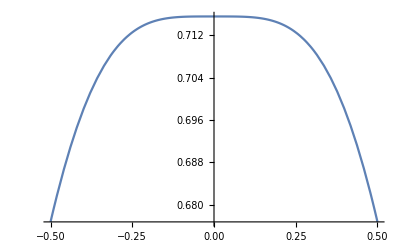

```mathematica
Plot[MagField,{z,-R/2,R/2}]
```

## Problem 2

```mathematica
deltau=(40*Pi)/200;
```

```mathematica
deltalx=−Sin[u]*deltau;
deltaly=Cos[u]*deltau;
deltalz=(0.05/Pi)*deltau;
deltal={deltalx,deltaly,deltalz};
rx=x-Cos[u];
ry=y-Sin[u];
rz=z-0.05/Pi*u;
r={rx,ry,rz};
```

```mathematica
B=Sum[u0*Ic/(4*Pi)*Cross[{−Sin[u]*deltau,Cos[u]*deltau,(0.05/Pi)*deltau},{x-Cos[u],y-Sin[u],z-0.05/Pi*u}]/(Norm[{x-Cos[u],y-Sin[u],z-0.05/Pi*u}])^3,{u,-20*Pi,20*Pi,deltau}]
```

{(-0.628319-0.01 y+(π z)/5)/(4 π (Abs[-1+x]^2+Abs[y]^2+Abs[-1.+z]^2)^(3/2))+199+(0.628319-0.01 y+(π z)/5)/(4 π (Abs[-1+x]^2+Abs[y]^2+Abs[1.+z]^2)^(3/2)),1,(π/5-(π x)/5)/(4 π (Abs[-1+x]^2+Abs[y]^2+Abs[1]^2)^(3/2))+(π/5-(π x)/20-(π x)/(4 √5)+1/5 √(5/8-(√5)/8) π y)/(4 π (Abs[1]^2+1^2+1^2)^(3/2))+(π/5+1/20-1+1/5 √(5/8+1) π y)/(4 π (1)^(3/2))+195+1/1+(π/5-(π x)/20-(π x)/(4 √5)-1/5 √(5/8-(√5)/8) π y)/(4 π (1)^(3/2))+(π/5-(π x)/5)/(4 π (Abs[1]^2+1^2+Abs[1]^2)^(3/2))}
 |  |  |  |

```mathematica
VectorPlot3D[B,{x,-1.5,1.5},{y,-1.5,1.5},{z,-1.5,1.5},VectorPoints->{12,12,12}]
```

-Graphics3D-

```mathematica
VectorPlot3D[B,{x,-1.5,1.5},{y,-1.5,1.5},{z,-1.5,1.5},VectorPoints->{12,12,12}]
```

-Graphics3D-

```mathematica
VectorPlot3D[B,{x,-1.5,1.5},{y,-1.5,1.5},{z,-1.5,1.5},VectorPoints->{12,12,12}]
```

-Graphics3D-